```mathematica
Integrate[x^k/(1+Exp[x-η]),{x,0,Infinity}]
```

ConditionalExpression[-Gamma[1+k] PolyLog[1+k,-ⅇ^η],Re[k]>-1]

```mathematica
k=1
```

1

```mathematica
-Gamma[1+k] PolyLog[1+k,-ⅇ^η]+Gamma[1+k] PolyLog[1+k,-ⅇ^-η]
```

PolyLog[2,-ⅇ^-η]-PolyLog[2,-ⅇ^η]

```mathematica
FullSimplify[%]
```

-PolyLog[2,-ⅇ^η]+PolyLog[2,-Cosh[η]+Sinh[η]]

```mathematica
F1[k_,η_]:=Integrate[x^k/(1+Exp[x-η]),{x,0,Infinity},Assumptions->k>-1]
```

```mathematica
F2[k_,η_,nMAX_]:=k! Exp[η] Sum[(-Exp[η])^(i-1)/i^(k+1),{i,1,nMAX},Assumptions->η<0]
```

```mathematica
fFermiZERO=Function[{k},2^-k (-1+2^k) Gamma[1+k] Zeta[1+k](*  Integrate[x^k/(1+Exp[x]),{x,0,Infinity}]*)];
```

```mathematica
fFermi=Function[{k,η,θ},NIntegrate[x^k Sqrt[1+θ x/2]/(1+Exp[x-η]),{x,0,Infinity},WorkingPrecision->128,Method->"DoubleExponential",MaxRecursion->16]]; (* Reference numerical result *)
```

```mathematica
(* Estimate of infinite sum; disretization error *)
fFermiSum=Function[{k,η,θ,h},Module[{x,dx,integrand,t,i,n},
t=i*h;
x=Exp[t-Exp[-t]];
dx=x*(1+ⅇ^-t);
integrand=x^k Sqrt[1+θ x/2]/(1+Exp[x-η]) dx;
oldSum=1;
newSum=0;
n=0;
While[newSum≠oldSum,
n++;
oldSum=newSum;
newSum=Sum[integrand,{i,-n,n}];
];
h*newSum
]
];
```

```mathematica
err=ParallelTable[fFermiSum[4,1,1,N[i/128,128]]-fFermi[4,1,1],{i,1,128,1}]
```

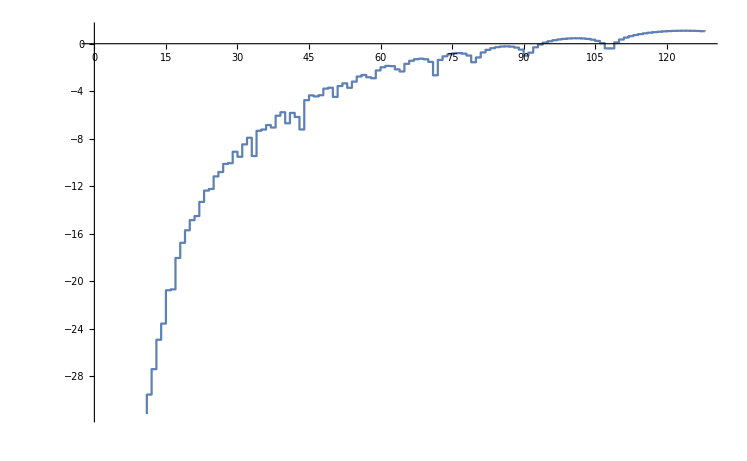

```mathematica
ListPlot[err//Abs//Log10,InterpolationOrder->0,Joined->True]
```

```mathematica
Table[i/128,{i,1,128,64}]
```

```mathematica
conv={{1,1/2,1/4,1/8,1/16,1/32,1/64},{-10.602286001068377269539464904898469146434280738571744712478811051928595925377391000202047433717889705165360149046512248951026079579869368`125.49614095997657,-0.004601677191217394813407714093308858231049112435784305431388264457424071352038495342915263935607952317897987472720917072837960084082789`122.20141664128946,-1.1916052860746094386852162878547207326849530529234917334593031617994285178237643762216781389633378699270529666807154849848895543`116.61447573791871*^-8,-1.989785694595770373977102053416677731369122164676446962593700830949273011913106602611801681869458119595076689828186`103.83714952988655*^-21,-9.90520981032373969082369815137588992118881472652476157771511801955206076519472824329623079916`82.53420687636763*^-43,-6.79880674294454139868054717239077605572946054304`37.37077588620571*^-88,0``124.53834318783488}//Abs}//Transpose;
```

```mathematica
conv//N//TableForm//TeXForm
```

\begin{array}{cc}
 1. & 10.6023 \\
 0.5 & 0.00460168 \\
 0.25 & \text{1.1916052860746094$\grave{ }$*${}^{\wedge}$-8} \\
 0.125 & \text{1.9897856945957703$\grave{ }$*${}^{\wedge}$-21} \\
 0.0625 & \text{9.90520981032374$\grave{ }$*${}^{\wedge}$-43} \\
 0.03125 & \text{6.798806742944541$\grave{ }$*${}^{\wedge}$-88} \\
 0.015625 & 0. \\
\end{array}

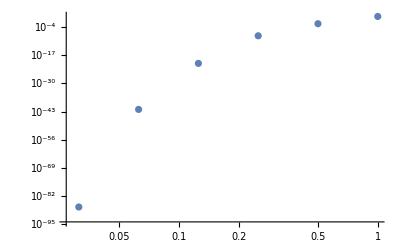

```mathematica
ListLogLogPlot[conv]
```

```mathematica
conv2={{1,1/2,1/4,1/8,1/16,1/32,1/64},conv[[;;,2]]//Abs//Log10}//Transpose;
```

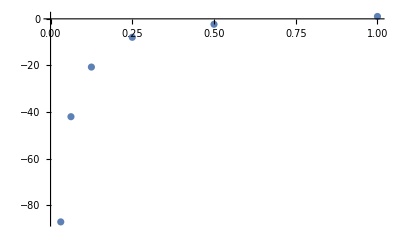

```mathematica
w1=ListPlot[conv2]
```

```mathematica
fit=a k^2+b k +c/.FindFit[conv2[[1;;4]],a k^2+b k +c,{a,b,c},k]
```

0.777087414029782576089804063103276303151551654866802118989865562648026336461222911662710127501863940207804+0.0155242728354868417153967784538551018392061602123661202005467506223925410688953185231805819271909720503225 k-2.3537106877794552198576363721102225820736161279282372805608719830405165425633176415556857189990191456242 k^2

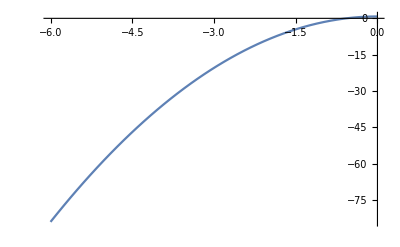

```mathematica
w2=Plot[fit,{k,-6,0}]
```

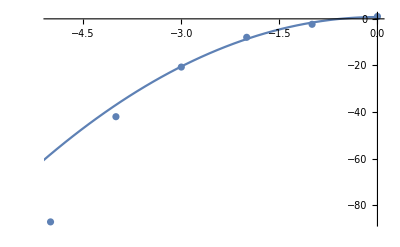

```mathematica
Show[w1,w2]
```

```mathematica
fFermi[4,1,1]
```

114.06687799137902589992508824775903265360960251309372394266372713106403373794999046746440912671766590817078780479429221800302036

```mathematica
fFermiTanhSinh=Function[{k,η,θ,h,tMAX},Module[{x,dx,integrand,tTBL},
x=Exp[t-Exp[-t]];
dx=D[x,t];
integrand=x^k Sqrt[1+θ x/2]/(1+Exp[x-η]) dx;
tTBL=Table[t,{t,-tMAX,tMAX,h}];
h*Sum[integrand,{t,tTBL}]
]
];
```

```mathematica
fFermiTanhSinh2=Function[{k,η,θ,h,tMAX},Module[{x,dx,integrand,tTBL},
x=η Exp[t-Exp[-t]];
dx=D[x,t];
integrand=x^k Sqrt[1+θ x/2]/(1+Exp[x-η]) dx;
tTBL=Table[t,{t,-tMAX,tMAX,h}];
h*Sum[integrand,{t,tTBL}]
]
];
```

```mathematica
N[fFermiTanhSinh[0,100,1,1/64,6],32]
```

484.34158778738602302779318960307

```mathematica
N[fFermiTanhSinh2[0,100,1,1/128,3],32]
```

484.34138234175278131129891601245

```mathematica
fFermi[0,100,1]
```

484.34138880192028335672358292907103190052599475005909232004399158562173234955193646764724511015023266744721800380934928429774535

```mathematica
%-%%
```

-0.000198985465739671069606674

```mathematica
0.000000 100.000000 1.000000 4.843413696289062500e+02 4.978699684143066406e+00 4.843413888019202886e+02
```

```mathematica
gFermi=Function[{n,α,β},
1/α^(3+2n)NIntegrate[x^(2n+1)Sqrt[x^2-α^2]/(1+Exp[x-β]),{x,α,Infinity},WorkingPrecision->128,Method->"DoubleExponential",MaxRecursion->16]];
```

```mathematica
kVALS=Rationalize[{-0.99999999999999988897769753748435,-0.999999,-0.9999,-0.999,-0.99,-0.98,-0.97,-0.96,-0.95,-0.94,-0.93,-0.92,-0.91,-0.9,-0.8,-0.7,-0.6,-0.5,0.0,0.5,1.0,2.0,4.0},0]//Reverse
```

{4,2,1,1/2,0,-1/2,-3/5,-7/10,-4/5,-9/10,-91/100,-23/25,-93/100,-47/50,-19/20,-24/25,-97/100,-49/50,-99/100,-999/1000,-9999/10000,-999999/1000000,-9007199254740991/9007199254740992}

```mathematica
For[i=1,i≤Length[kVALS],i++,
Print[Date[]];
Print[i,"\t",kVALS[[i]],"\t",fFermi[kVALS[[i]],0,0]]
]
```

{2020,3,22,14,14,0.2288902}

1	4	27034.313115148352229987987344983505332337555742937804825979968880808517207988842107400052758922952940491638674506062993631103445

{2020,3,22,14,14,0.2949501}

2	2	366.2321054696421055583148799189747393104776055050779729117217304627689022922914815050436108848092215053724426404133557936221372

{2020,3,22,14,14,0.3650139}

3	1	51.644888667433741960137179191460838358676316823200522785241874763866679041494814735570513069457418048401926053577440568865131306

{2020,3,22,14,14,0.4350774}

4	1/2	21.344471492355182949415216846456046737933425614757223745684755209293414021438960693242161170532458462670278184434739757002729098

{2020,3,22,14,14,0.5171516}

5	0	10.000045398899216864646769487829307105596781502281787558794264063195488918050659008858761958351231476298973413202258914807306332

{2020,3,22,14,14,0.5912254}

6	-1/2	6.2971372445338478441640968437168485503012319294691589388830918979537128407861127147573511914026822461388199131574837688699527013

{2020,3,22,14,14,0.7303452}

7	-3/5	6.2533853290857552294733265561473844472893095028025108014166914561701644474666859380880615001025575697551202248886296925269025228

{2020,3,22,14,14,0.8974967}

8	-7/10	6.6262589153140938474634960330050291608508749707921823364445493955000775490490211981550538789393392578129273556298356368576024625

{2020,3,22,14,14,1.079662}

9	-4/5	7.9018656569956551999898160582332370557152279648659686156169841212074374379469295891408284754100740983607586940729147577555158244

{2020,3,22,14,14,1.26483}

10	-9/10	12.56864756799700371412446545493255840926943874779137321247324579412234444171325763328540298436727099406067524093189515291702566

{2020,3,22,14,14,1.491036}

11	-91/100	13.649219455490328048437249180214509387399803463564753667379853821266791917732666844097452881530215522598623820944994466693080303

{2020,3,22,14,14,1.75989}

12	-23/25	15.008032043776149605866981307081778707401616814369241503466130992784847770465065358373413311311838568223638119117661619915230987

{2020,3,22,14,14,2.0181244}

13	-93/100	16.764119223382855461562874401431831637212582012846336066719943608489744530807174041925138571005445223526146365941551298199092561

{2020,3,22,14,14,2.3068912}

14	-47/50	19.115876516796326619030749099778368167527416399317530909530019872175846889811082522691954767219349584847164121940429906891163017

{2020,3,22,14,14,2.6071634}

15	-19/20	22.420422551780865474850700768408811927396959689831657207795674934711057139207783321853621079992731621127816943154051887275517946

{2020,3,22,14,14,2.9134413}

16	-24/25	27.392002749300771434293681552269983979510525240114506682916138473538002482788408708205943000887281313366690145957314095484393355

{2020,3,22,14,14,3.2727673}

17	-97/100	35.697200393299992798449112985664593570243333183658042113210152922004127434912997630403899563234589652594164213904231884480806029

{2020,3,22,14,14,3.735187}

18	-49/50	52.335780918632084629695705386124272160403302240145441681318850257301444299254202945132314013387723687818279796974076648588642453

{2020,3,22,14,14,4.4288263}

19	-99/100	102.30660194378047896508052553095328940857793902085985029744494661819622557632041871057601437466628450885121827988653731857565099

{2020,3,22,14,14,6.2505138}

$Aborted

```mathematica
tbl1=N[Table[2^-k (-1+2^k) Gamma[1+k] Zeta[1+k],{k,kVALS}],64]
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{23.33087449072582334245572344528326878128432068879303826941933525,1.803085354739391428099607242267174986147479438510748322688407333,0.8224670334241132182362075833230125946094749506033992188677791147,0.6780938951531010073123088519165904556504522548947857136527470469,Indeterminate,1.072154929940191339530897446575632665786377507637416078164503193,1.29814241965106956795921584123635721641264009394176863560414203,1.689942082069844217686714770602930900671201078330503565666824674,2.497004078476951397980741569014232323613084668100192052427635646,4.968622353012584681311135630641922951927995958824210671724293419,5.521189921826484211173541527105669107259482772150263823325043502,6.212615000264106719757001109317667812789443462761104095436771924,7.102420248123802260268297125741419490002855686513881861199828704,8.289810824818017391611680436050382019207377171943772474496387767,9.953356927101239824295276322308958584397086426908057517889879027,12.45020013620965502325106248545318882757654770445560577038149347,16.6136724632937745042063201522578515991506679819765844888675178,24.94377253758025291812015233827140817253031233419577803501199377,49.94049893725401506813660842804194247203770866958669469004588715,499.9375169868556689643081293763321470615725587202878944182177892,4999.937216886339042464251639049043273589221236358978525979738903,499999.9371838538768643182303373528136234527851331262237984545916,4.503599627370495937183520193961039106109848969713978604528170591×10^15}

```mathematica
4999.937216886339042464251639049043273589221236358978525979738902773981302806377991405257805986021478437297040296113910525408834161116416613`128.-4999.93721688633904246425163904904327358922123635897852597973890277398130277450021`64.
```

0.

```mathematica
SetDirectory["/home/misiek/programy/biblioteki/libfermidirac/src"]
```

SetDirectory::cdir: Cannot set current directory to /home/misiek/programy/biblioteki/libfermidirac/src.

$Failed

```mathematica
SetDirectory["H:\\misiek/programy/biblioteki/libfermidirac/src"]
```

H:\misiek\programy\biblioteki\libfermidirac\src

```mathematica
Install["Fermi-Dirac"]
```

LinkOpen::linke: Could not find MathLink executable.

$Failed

```mathematica
?FFermi
```

Global`FFermi

FFermi[k_?NumericQ,eta_?NumericQ,theta_?NumericQ]:=ExternalCall[LinkObject['/home/misiek/programy/biblioteki/libfermidirac/src/Fermi-Dirac',155,4],CallPacket[0,{k,eta,theta}]]

```mathematica
Table[FFermi[k,0.0,0.0],{k,N@kVALS}]
```

{4.5036×10^15,500000.,4999.94,499.938,49.9405,24.9438,16.6137,12.4502,9.95336,8.28981,7.10242,6.21262,5.52119,4.96862,2.497,1.68994,1.29814,1.07215,0.693147,0.678094,0.822467,1.80309,23.3309}

```mathematica
Table[1/2/(k+1),{k,kVALS}]//N
```

{4.5036×10^15,500000.,5000.,500.,50.,25.,16.6667,12.5,10.,8.33333,7.14286,6.25,5.55556,5.,2.5,1.66667,1.25,1.,0.5,0.333333,0.25,0.166667,0.1}

```mathematica
FFermi[-1.0+$MachineEpsilon,0.0,0.0]
```

2.2518×10^15

```mathematica
Series[2^-k (-1+2^k) Gamma[1+k] Zeta[1+k],{k,-1,2}]
```

1/(2 (k+1))+1/2 (-EulerGamma-2 Log[2]+Log[2 π])+1/16 (π^2+16 EulerGamma Log[2]+12 Log[2]^2+8 Log[2] Log[π]+4 Log[π]^2-8 EulerGamma Log[2 π]-16 Log[2] Log[2 π]-8 StieltjesGamma[1]) (k+1)+1/48 (-3 EulerGamma π^2-6 π^2 Log[2]-36 EulerGamma Log[2]^2-32 Log[2]^3-24 EulerGamma Log[2] Log[π]-48 Log[2]^2 Log[π]-12 EulerGamma Log[π]^2-24 Log[2] Log[π]^2+3 π^2 Log[2 π]+48 EulerGamma Log[2] Log[2 π]+24 Log[2]^2 Log[2 π]+4 Log[2 π]^3+4 PolyGamma[2,1]+48 Log[2] StieltjesGamma[1]-24 Log[2 π] StieltjesGamma[1]-12 StieltjesGamma[2]+8 Zeta[3]) (k+1)^2+O[k+1]^3

```mathematica
X={RandomReal[30],RandomReal[{-2000,2000}],RandomReal[10]}
```

{0.0391559,-1443.62,1.90499}

```mathematica
FFermi@@X
```

0.

```mathematica
fFermi@@X
```

NIntegrate::precw: The precision of the argument function (√1 + 0.952497\ x\ x^0.0391559/1 + ⅇ^1443.62  + x) is less than WorkingPrecision (128.).

1.4964879862141293870453972570594291426917332188817650808729514129915683123844073180999012418679053621779153747942258780670507068×10^-627

```mathematica
{FFermi@@X/fFermi@@X}-1
```

NIntegrate::precw: The precision of the argument function (√1 + 0.952497\ x\ x^0.0391559/1 + ⅇ^1443.62  + x) is less than WorkingPrecision (128.).

{-1.}

```mathematica
gFermi[1.0,1.0,1.0]
```

NIntegrate::precw: The precision of the argument function (x^3.\ √-1. + x^2/1 + ⅇ^-1. + x) is less than WorkingPrecision (128.).

58.676

```mathematica
?GFermi
```

Global`GFermi

GFermi[n_?NumericQ,alpha_?NumericQ,beta_?NumericQ]:=ExternalCall[LinkObject['/home/misiek/programy/biblioteki/libfermidirac/src/Fermi-Dirac',155,4],CallPacket[1,{n,alpha,beta}]]

```mathematica
GFermi[1.0,1.0,1.0]
```

58.676

```mathematica
%/%%
```

{58.676/Null}

```mathematica
%-1
```

{-1+58.676/Null}

```mathematica
gPlus=Function[{n, α,β},gFermi[n,α,-β]];
```

```mathematica
gMinus=Function[{n, α,β},gFermi[n,α,β]];
```

```mathematica
gPlus[1,1,1]
```

8.3549674906883717534606844431248880928231220502336444056755714845070226926133875853400416916980184011433639053145467658459488234

```mathematica
gMinus[1,1,1]
```

58.676001573385478663496785571226902432064887893274314523865895386795270715573512173470827164870264151085024829902019262006371836

```mathematica
FFermi[0.5,0.5,2.0]
```

1.6133

```mathematica
?FFermi
```

Global`FFermi

FFermi[k_?NumericQ,eta_?NumericQ,theta_?NumericQ]:=ExternalCall[LinkObject['/home/misiek/programy/biblioteki/libfermidirac/src/Fermi-Dirac',155,4],CallPacket[0,{k,eta,theta}]]

```mathematica
?NumberQ
```

RowBox[{"NumberQ", "[", StyleBox["expr", "TI"], "]"}] gives True if StyleBox["expr", "TI"] is a number, and False otherwise.

```mathematica
Attributes[FFermi]
```

{}

```mathematica
SetAttributes[FFermi,NumericFunction]
```

```mathematica
NumericQ[Pi]
```

True

```mathematica
FFermi[Pi,0,2]
```

15.383

```mathematica
fFermi[Pi,0,2]
```

15.382960307741615424292742337691474914068174467905868780227602999731687810622302367154909116101185757333371887780389005822713216

```mathematica
GFermi[1,1,1]
```

58.676

```mathematica
fFermi[1/2,1/2,2]
```

1.6133041280152989835357214307050531001871878393296800106436991810894216603332833969311107189006814887810249818533370759354074066

```mathematica
gFermi[1/2,10^1,2]
```

0.000018545935774538557966847373787251950734638440862245657151848079158123980220206511214597504556593019790967481857997593516378760446

```mathematica
cmp=Table[{SetPrecision[GFermi[1/2,10^lgeta,2],128],(If[MachineNumberQ[N[#]],#,0.]&)[gFermi[1/2,10^lgeta,2]]},{lgeta,-4,4,1/2}]
```

{{3.42982832455528512×10^17,3.4298283245552852095569481299883124961361463308229776600159638402015116464357325563096690369972523714729586340732830151383756456×10^17},{3.429828308742637×10^15,3.4298283087426370964122748949023749229053173829998350442072923743399166251271852850893496356960113622846416847915729485485450901×10^15},{3.429828150616078515625×10^13,3.4298281506160790950689514011214732315207383699390426380114856301037038801092073199882365709382440112509582280401397946205659025×10^13},{3.4298265693439404296875×10^11,3.4298265693439414975022257690935625964413708318126791586127296272456094875667213667339000481987642148470747005448422485494838772×10^11},{3.42981075607974910736083984375×10^9,3.4298107560797488862912765580935968921950063483064820892079954260047788692852638307314975406351894918424707356296862824467605922×10^9},{3.42965258045133054256439208984375×10^7,3.4296525804513317429473030112565045751023245138718067807200941529936607651040489467189308304954671140057729233940755467608677248×10^7},{342806.7655799280037172138690948486328125,342806.76557992805594890734133346296998465455940245912464460613922662440501633124474622962449143644042407341454069307978379711676},{3412.0151314086442653206177055835723876953125,3412.0151314086439540279638536643978946216433300300497637461387967092897407188449421051070978804862574913027953887607874884278681},{32.42794951914263634762392030097544193267822265625,32.427949519142632348713944103363835798899740828817571764472356634590677923198399550021936479058784319922986558093500446435862582},{0.17620725952176619077960140202776528894901275634765625,0.17620725952176625816180391665489494387533373960816975561765506166397763096753150019246201425123870582598230029297779871831606303},{0.0000185459357745385589326565789480838475355994887650012969970703125,0.000018545935774538557966847373787251950734638440862245657151848079158123980220206511214597504556593019790967481857997593516378760446},{1.069742389261364752040684883142516059327165500909828654840794115443713963031768798828125×10^-15,1.0697423892613675728094294842110674751154623174429300497496937391484345572949627837443895293371851993965619605859165153297262487×10^-15},{3.5632692225001078960294402147321603418938167964675216392456579518859631781238031963795954481883245058473625976113254888721915137×10^-46,3.5632692225001083168494643833425186401661474711525548331581071518593322240155849407256515552453405801942912257288107096146453294×10^-46},{7.67908239608315989854317812835711345515253309412795418462850952099632578879615470256969335551608125033248302856792161796085344×10^-141,7.6790823960834114528975340345856911467401968478714350182995415867929876657184134174681806100300248434815475250660425887472112693×10^-141},{0,0.},{0,0.},{0,0.}}

```mathematica
Table[(#1/#2-1&)@@cmp[[k]],{k,1,Length[cmp]}]//Abs//Log10
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{-16.58317309703813777351585117675901634361786964273992274794829913063512078976951086231315974758005463123624944777,-16.55114005018497887020374766622139745322224260924130363548726625850975209021662753683150597342896208520592811273,-15.772260926749461111455794205889013974430059321457803478555145152024011849652869019395936412934474918135502282745,-15.506776254580889924881646366841124922742857643888166045833610611097957950351363907767516238185151528067146843044,-16.190741204673739650061109305829195901114220214621236251708443671439485826353956542186469674475871599773651410811,-15.455930324753075768738554267346705419205555586092883809861257090188273356750638263486364096970848802371361071381,-15.817115277606458736384257353251966458820152733869171379945832823432270018595297189391844472094140550895742193689,-16.039842076530073191055223746280481191159264205440900585234895443671868343305886321908691806981681584687710371008,-15.908977860906793084020686339117065906839640852722964217352814970301976146917368281636492208817613396922253022037,-15.417478594228648567582419921661222810404394399227139701382409067528888588355155480887938439480650820779698400725,-16.28335741110728424351292993986511676070699637990107979681454122970859863834240378898868645786411099837136396445,-14.5789117225541874862862855336347656353145923458866832091370608191231538440356287191062369173589788419261895480369,-15.927752239702593921318770906579376797709184681960200074457268163719999537306635384745969088537286474319423683996,-13.48467748828909212370559416930176836386260034828445072585262487666603373445174760330265929180032571603038691486121,Indeterminate,Indeterminate,Indeterminate}

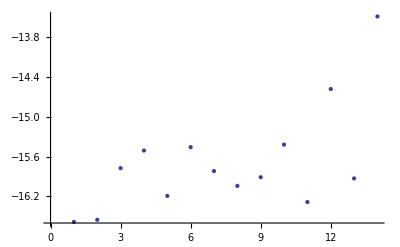

```mathematica
ListPlot[%]
```

```mathematica
$MachineEpsilon
```

2.22045×10^-16

```mathematica
?N
```

N[expr] gives the numerical value of expr. 
N[expr,n] attempts to give a result with n-digit precision.

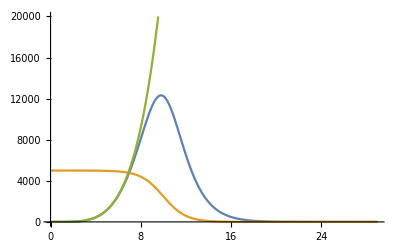

```mathematica
Block[{k=4,θ=1,η=10},Plot[{x^k Sqrt[1+θ x/2]/(1+Exp[x-η]),5000/(1+Exp[x-η]),x^k Sqrt[1+θ x/2]},{x,0,29},PlotRange->{0,20000}]]
```

```mathematica
x^k Sqrt[1+θ x/2]/(1+Exp[x-η])/.{k->4,θ->1,η->1,x->1}
```

(√(3/2))/2

```mathematica
N[%]
```

0.612372

```mathematica
Limit[Exp[t-Exp[-t]+η],t->-Infinity]
```

0

```mathematica
D[η Exp[t-Exp[-t]],t]x^k Sqrt[1+θ x/2]/(1+Exp[x-η])/.x->η Exp[t-Exp[-t]]
```

(ⅇ^(-ⅇ^-t+t) (1+ⅇ^-t) η (ⅇ^(-ⅇ^-t+t) η)^k √(1+1/2 ⅇ^(-ⅇ^-t+t) η θ))/(1+ⅇ^(-η+ⅇ^(-ⅇ^-t+t) η))

```mathematica
D[η Exp[Sinh[t]],t]x^k Sqrt[1+θ x/2]/(1+Exp[x-η])/.x->D[η Exp[Sinh[t]],t]
```

(ⅇ^Sinh[t] η Cosh[t] (ⅇ^Sinh[t] η Cosh[t])^k √(1+1/2 ⅇ^Sinh[t] η θ Cosh[t]))/(1+ⅇ^(-η+ⅇ^Sinh[t] η Cosh[t]))

General::munfl: (3.09997×10^-289)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1111.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.21779×10^-181)^3 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

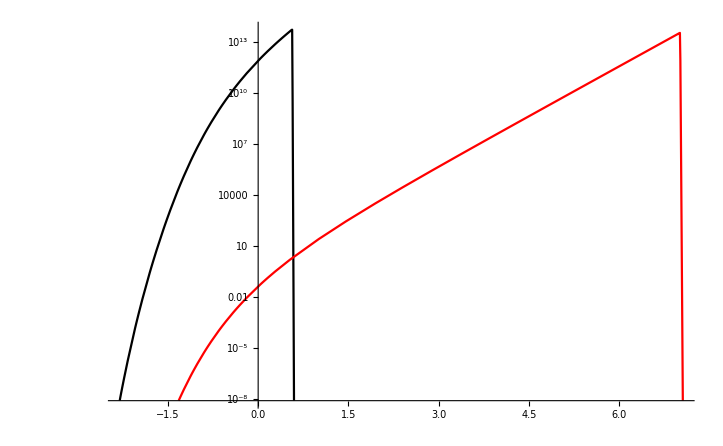

```mathematica
Block[{k=3,θ=1,η=1111},LogPlot[{(ⅇ^(-ⅇ^-t+t) (1+ⅇ^-t) η (ⅇ^(-ⅇ^-t+t) η)^k √(1+1/2 ⅇ^(-ⅇ^-t+t) η θ))/(1+ⅇ^(-η+ⅇ^(-ⅇ^-t+t) η)),((ⅇ^(-ⅇ^-t+t))^(1+k) (1+ⅇ^-t) √(1+1/2 ⅇ^(-ⅇ^-t+t) θ))/(1+ⅇ^(ⅇ^(-ⅇ^-t+t)-η))},{t,-6.5,16.5},PlotRange->{2^-27,All},PlotStyle->{Black,Red}]]
```

```mathematica
Reduce[x^5==x+5,x]
```

x==Root1.45Root[-5-#1+#1^5&,1]1.4519028714517146||x==Root-1.09-0.734 ⅈRoot[-5-#1+#1^5&,2]-1.0941779906641493||x==Root-1.09+0.734 ⅈRoot[-5-#1+#1^5&,3]-1.0941779906641493||x==Root0.368-1.36 ⅈRoot[-5-#1+#1^5&,4]0.36822655493829215||x==Root0.368+1.36 ⅈRoot[-5-#1+#1^5&,5]0.36822655493829215

General::munfl: (2.43537×10^-292)^(5/3) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (6.28554×10^-225)^(5/3) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.43537×10^-292)^(5/3) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

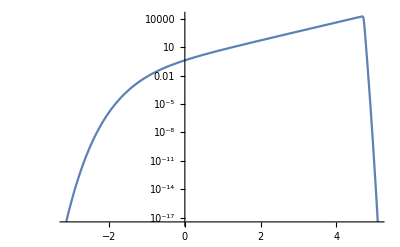

```mathematica
Block[{k=2/3,θ=1,η=111},LogPlot[((ⅇ^(-ⅇ^-t+t))^(1+k) (1+ⅇ^-t) √(1+1/2 ⅇ^(-ⅇ^-t+t) θ))/(1+ⅇ^(ⅇ^(-ⅇ^-t+t)-η)),{t,-6.5,6.5},PlotRange->{$MachineEpsilon/2^6,All},GridLines->{{Log[η]+ProductLog[1/η]},None}]]
```

```mathematica
Solve[Exp[t-Exp[-t]]==η,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→Log[η]+ProductLog[1/η]}}

```mathematica
N[%]
```

{{t→4.71846}}

```mathematica
D[x^(k+1/2)Exp[-x],x]
```

ⅇ^-x (1/2+k) x^(-1/2+k)-ⅇ^-x x^(1/2+k)

```mathematica
Solve[%==0,x]
```

{{x→1/2 (1+2 k)}}

```mathematica
Block[{k=4,η=10,θ=1},{k+0.5,x/.NMaximize[{x^k Sqrt[1+θ x/2]/(1+Exp[x-η]),x>0},x][[2]]}]
```

{4.5,9.80126}

```mathematica
D[x^(k) /(1+Exp[x-η]),x]
```

(k x^(-1+k))/(1+ⅇ^(x-η))-(ⅇ^(x-η) x^k)/((1+ⅇ^(x-η))^2)

```mathematica
Solve[%==0,x]//Expand
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→k+ProductLog[ⅇ^(-k+η) k]}}

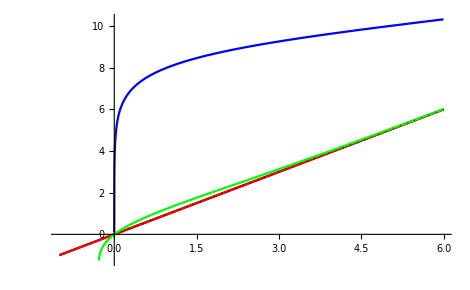

```mathematica
Plot[Evaluate@Table[k+ProductLog[ⅇ^(-k+η) k],{η,{-100,-10,0,10}}],{k,-1,6},PlotStyle->{Black,Red,Green,Blue,Yellow},Epilog->{Dotted,Line[{{0,0},{6,6}}]}]
```

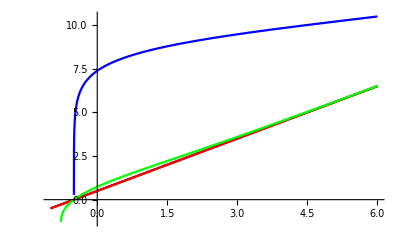

```mathematica
Plot[Evaluate@Table[k+1/2+ProductLog[ⅇ^(-k+η-1/2) (k+1/2)],{η,{-100,-10,0,10}}],{k,-1,6},PlotStyle->{Black,Red,Green,Blue,Yellow}]
```

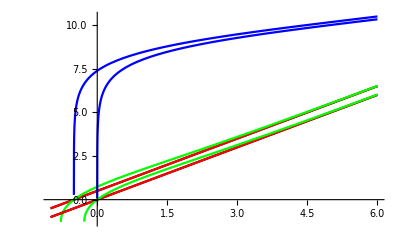

```mathematica
Show[%,%%]
```

```mathematica
Series[k+ProductLog[ⅇ^(-k+η) k],{η,-Infinity,2}]
```

k+ⅇ^(η-k+O[1/η]^3) k-ⅇ^(2 η-2 k+O[1/η]^3) k^2+3/2 ⅇ^(3 η-3 k+O[1/η]^3) k^3-8/3 ⅇ^(4 η-4 k+O[1/η]^3) k^4

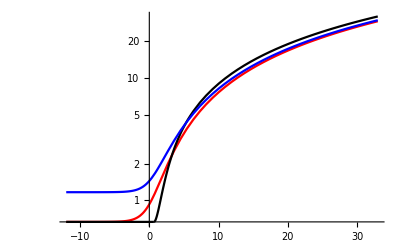

```mathematica
Block[{k=2/3},LogPlot[{k+ProductLog[ⅇ^(-k+η) k],If[η≤k,k,η+Exp[k-η]-1 ],k+1/2+ProductLog[ⅇ^(-k+η-1/2) (k+1/2)]},{η,-12,33},PlotStyle->{Red,Black,Blue}]]
```

```mathematica
D[k+ProductLog[ⅇ^(-k+η) k],η]
```

ProductLog[ⅇ^(-k+η) k]/(1+ProductLog[ⅇ^(-k+η) k])

```mathematica
Log[2.^-26]
```

-18.0218

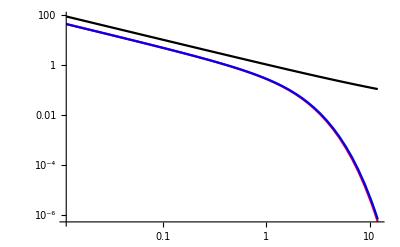

```mathematica
Block[{k=-0.999,θ=0.1,η=0},LogLogPlot[
{
x^k /(1+Exp[x-η]),
x^k Sqrt[1+θ x/2]/(1+Exp[x-η]),
x^k Sqrt[1+θ x/2]
},{x,0,12},PlotRange->All,PlotStyle->{Red,Blue,Black}
]]
```

```mathematica
kVALS[[1;;20]]
```

{4,2,1,1/2,0,-1/2,-3/5,-7/10,-4/5,-9/10,-91/100,-23/25,-93/100,-47/50,-19/20,-24/25,-97/100,-49/50,-99/100,-999/1000}

```mathematica
Integrate[x^k/(1+Exp[x-η]),{x,0,Infinity}]
```

ConditionalExpression[-Gamma[1+k] PolyLog[1+k,-ⅇ^η],Re[k]>-1]

```mathematica
AsymptoticIntegrate[x^k/(1+Exp[x-η]),{x,0,Infinity},{k,-1,1}]
```

-(ⅇ^η EulerGamma)/(1+ⅇ^η)+ⅇ^η/((1+ⅇ^η) (1+k))-PolyLog^(1,0)[0,-ⅇ^η]+(1+k) ((ⅇ^η (EulerGamma^2+π^2/6))/(2 (1+ⅇ^η))+EulerGamma PolyLog^(1,0)[0,-ⅇ^η]-1/2 PolyLog^(2,0)[0,-ⅇ^η])

```mathematica
Table[{(-(ⅇ^η EulerGamma)/(1+ⅇ^η)+ⅇ^η/((1+ⅇ^η) (1+k))),fFermi[k,1,0]+Gamma[1+k] PolyLog[1+k,-ⅇ^η]},{k,kVALS[[1;;20]]}]/.η->0//TableForm
```

1/10-EulerGamma/2 | 37.63857588144082789474607345574213789148119950648917223364903585250063642850386325038809295979545569979101559325086852164437636
1/6-EulerGamma/2 | 2.525245870886010296214667309918045327288162155952545165781779457551465148915711170209150097980445704461731218391163990973243153
1/4-EulerGamma/2 | 0.9838190370206610384147938435960863849484990669888318215877144426134693952547630069347168139670712001678405972036440743874210334
1/3-EulerGamma/2 | 0.7182813855134631190073252699849335558928986924511568905859877377985139586394937167561961411650651791438275992847136627122182782
1/2-EulerGamma/2 | 0.6201145069582775246317633735096790738397799513100931205983835053438012795394925053303370792808737038470195657948936677882697395
1-EulerGamma/2 | 0.7482564272067713035106188901150742652776217735682134372725194577803906789212653619943238198343061247139792390453434811475386676
5/4-EulerGamma/2 | 0.849205424985015163238993910618681276674223816951558555860208840429420745925528864414090464433818415576886492087031502699766812
5/3-EulerGamma/2 | 1.028875161496265317944216329440022524184772577472196115313830410903671371463082111570533901479303434320099013033060894395393065
5/2-EulerGamma/2 | 1.402743517310365067572829709955165049867161067197934392255378924642481242980659370562842374428544169971077920232413259895440099
5-EulerGamma/2 | 2.548455076513539017471294263743016434845808021510109990066859190141488332394754035138949247708845546864670702432271369569052382
50/9-EulerGamma/2 | 2.804321080887440394456625960975562812171649150153224286235735139745370751082144544529462007759256485091143859223781148542598136
25/4-EulerGamma/2 | 3.124387165072316514096218963216039715102825021970465746859107408047559252421040025934868754383787274711245639417744807548925562
50/7-EulerGamma/2 | 3.536160416919085911772215439558922914107935635531236105841028177902956711340667035132336492908960866209110826484415966360240233
25/3-EulerGamma/2 | 4.08548591632360285837670737398518191400030815865395414213707720247230835702532391202210668384266908591224641731615937114656298
10-EulerGamma/2 | 4.854884718050912807399615114916884445254531941308611196411443699715698893737546372517477270418940935938711508559505593699334023
25/2-EulerGamma/2 | 6.009398808229907652210420068180457528547192527264963918050788751206125172657930408467187318996030580515356392357862151269010598
50/3-EulerGamma/2 | 7.934125973028334266634240123840671915853515977247258596533207198917134506800400125475328268018285678352219549022155086708946464
25-EulerGamma/2 | 11.78435927205157608011542510664817772618145112286318041714033293154410108036165390738296198847315625510508081233961446204588103
50-EulerGamma/2 | 23.33656334934215388030297611483973522436396023794664787792380921139188296804983008087030487685931920481504318768658712077143576
500-EulerGamma/2 | 231.2886474293373281224159389640682739840106106033393992103718018986170493319907730538424010860278411910914739399358925431850939